# Comparison between the triangle plaquette model and the triangle continuum model.

# Triangular Plaquette Model H = (2/g^2) E^2 + 2/g^2 B^2 ---> (2/g^2)(E1^2 +E2^2 + E3^2) + (1/g^2) (1 - Cos[theta1, +theta2 + theta3)) With commutators [E_i, e^{itheta_j}] = delta_[ij} e^{itheta_j}

```mathematica
(* All terms are positve: With Wilson Plaq
B^2(s) = (1/2)Tr[2 - U_p - U^\dag_p](s) 
 (B(s)_etra)^2 = \sum_s Tr[2 - U(s)U^\dag(s+1) - U(s+1)U^\dag(s)] 

For U(1) Qubits Links:    U      --> sigma^+ = (sigma^x + i sigma^y)/2
                        U^\dag --> sigma^- = (sigma^x - i sigma^y)/2

E(s) = sigma^z(s) +  sigma^z(s+1)

Conventions for Qubit kernel construction *)
```

```mathematica
(*Sigma operators*)
```

```mathematica
Sigma[0] = SparseArray[IdentityMatrix[2]];
Sigma[1] = SparseArray[{{0, 1}, {1, 0}}];
Sigma[2] = SparseArray[{{0, -I}, {I, 0}}];
Sigma[3] = SparseArray[{{1, 0}, {0, -1}}];
SigmaP= (Sigma[1]+ I*Sigma[2])/2;
SigmaM= (Sigma[1]- I*Sigma[2])/2;
```

```mathematica
(* Kronecker builds multi-Qubit tensor:  Left most matrix has fast  -- low bit -- convention 
Lables of N = nQubit tensor should be   sigma_{N} x sigma_{N-1} x  ... x  sigma_{0}   *)
```

```mathematica
(* Insert FullSigma[ a = sigma_type , j = postion = 0,1,..., nQubit-1] *)
```

```mathematica
FullSigma[ a_, j_, nQubit_]:=KroneckerProduct[IdentityMatrix[2^(nQubit-j -1)], Sigma[a], IdentityMatrix[2^j]]
MatrixForm[FullSigma[3, 1, 2]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

## Plaquette term

```mathematica
(*Single plaquette term at s-th layer *)
```

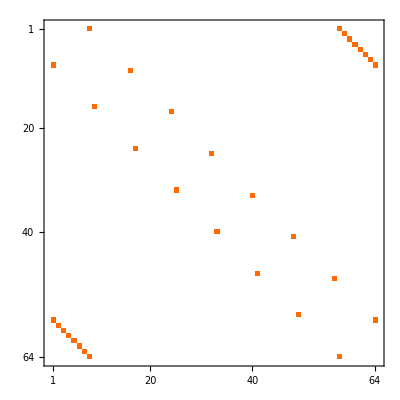

```mathematica
H3single[s_, nQubit_] := KroneckerProduct[ IdentityMatrix[2^(3*(s-1))],SigmaP, SigmaP, SigmaP,IdentityMatrix[2^(nQubit-3*s)]]+KroneckerProduct[IdentityMatrix[2^(3*(s-1))], SigmaM, SigmaM, SigmaM, IdentityMatrix[2^(nQubit-3*s)]];
(*Sum over all layers*)
H3s[nQubit_] := Sum[H3single[s, nQubit],{s,1,nQubit/3}]
MatrixPlot[H3s[6]]
```

## Electric links between neighborhood layers sigmaz_{j + 3} x sigmaz_j note + convention on Qubit operators

```mathematica
H1s[nQubit_] := Sum[FullSigma[3,Mod[j+3,nQubit], nQubit].FullSigma[3, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]
```

## XX + YY chain

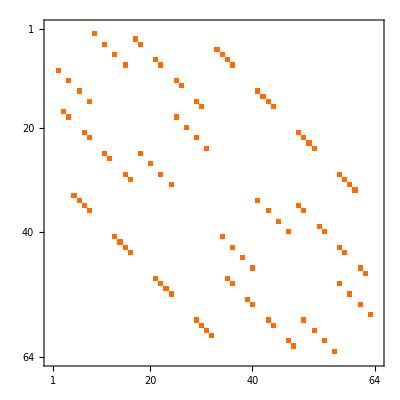

```mathematica
H2s[nQubit_] :=Sum[FullSigma[1,Mod[j+3,nQubit], nQubit].FullSigma[1, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]+
Sum[FullSigma[2,Mod[j+3,nQubit], nQubit].FullSigma[2, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]
MatrixPlot[H2s[6]]
```

## Define Hamiltonian

```mathematica
(* Sign are choosen to be "right" of Hamilton *)
```

```mathematica
H0[g_, alpha_, nQubit_]:=SparseArray[((g^2)/2)*H1s[nQubit]-  (alpha/(2*g^2))*H2s[nQubit] - (1/(2*g^2))*H3s[nQubit]]
```

```mathematica
H[g_, alpha_, nQubit_]:=SparseArray[((g^2)/2)*H1s[nQubit]-  (alpha/(2*g^2))*H2s[nQubit] - (1/(2*g^2))*H3s[nQubit]]+
((g^2 /2) nQubit  + 2 (alpha/(2*g^2))nQubit + ((nQubit/3)/(2g^2))) IdentityMatrix[2^nQubit]
```

```mathematica
Eigenvalues[H3s[6]]
```

{-2,2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Eigenvalues[H1s[6]]
```

{-6,-6,-6,-6,-6,-6,-6,-6,6,6,6,6,6,6,6,6,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
Eigenvalues[H2s[6]]
```

{-12,12,-8,-8,-8,-8,-8,-8,8,8,8,8,8,8,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

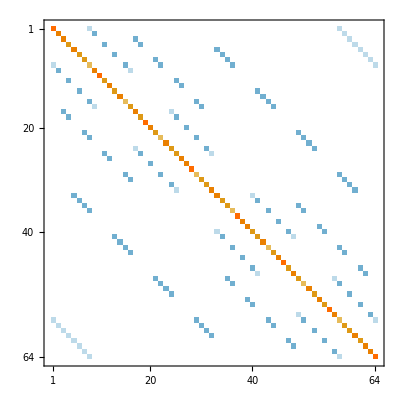

```mathematica
MatrixPlot[H[1, 1, 6]]
```

## Eigenvalue spectrum of H(g, alpha)

```mathematica
Eigs[g_, alpha_, nQubit_, k_] := Sort[Eigenvalues[H[g, alpha, nQubit], k], Less]
```

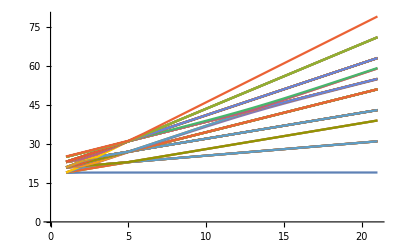

```mathematica
ListPlot[Transpose[Table[Eigs[1, c, 6, 2^6] +18, {c, 0, 5, 0.25}]], Joined->True]
```

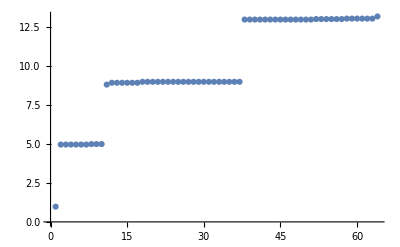

```mathematica
ListPlot[Eigs[1, 1,6 , 2^6]]
```

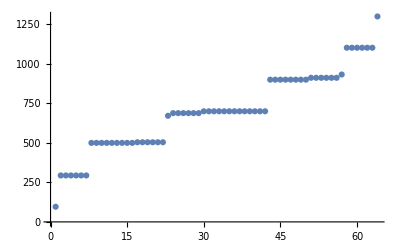

```mathematica
ListPlot[Eigs[0.1, 1,6 , 2^6]]
```

# Gauge Rotation Operators

```mathematica
(* Gauge Rotation Operators J12, J23, J31 *)
J12[nQubit_] := Sum[FullSigma[3,Mod[s*3+1,nQubit], nQubit]-FullSigma[3, Mod[s*3+2,nQubit], nQubit],{s,0,nQubit/3-1}]
J23[nQubit_] := Sum[FullSigma[3,Mod[s*3+2,nQubit], nQubit]-FullSigma[3, Mod[s*3+3,nQubit], nQubit],{s,0,nQubit/3-1}]
J31[nQubit_] := Sum[FullSigma[3,Mod[s*3+3,nQubit], nQubit]-FullSigma[3, Mod[s*3+1,nQubit], nQubit],{s,0,nQubit/3-1}]
```

```mathematica
NQubits = 12
```

12

## Eigenvalues (Diagonal Elements) of Gauge Rotation Operators

```mathematica
D12 = Normal[Diagonal[J12[NQubits]]];
```

```mathematica
D23 = Normal[Diagonal[J23[NQubits]]];
```

```mathematica
D31 = Normal[Diagonal[J31[NQubits]]];
```

```mathematica
(*Check if they sum up to zero *)
```

```mathematica
D12 + D23 + D31
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Permutation Rule Ordered by Square Sum Eigenvalues

```mathematica
perm = Ordering[D12^2+ D23^2+D31^2];
```

```mathematica
(* Count the number of zeros *)
```

```mathematica
NZero = Count[D12^2+ D23^2+D31^2, 0]
```

346

## The Permutated Hamiltonian Looks It Consists of Block Sectors with Sub-square Matrices

```mathematica
PermHamiltonian[g_, alpha_, nQubits_] := H[g, alpha, nQubits][[perm, perm]]
```

```mathematica
MatrixPlot[PermHamiltonian[0.1, 1, NQubits]]
```

-Graphics-

## The sub matrix with basis corresponding to zero eigenvalues

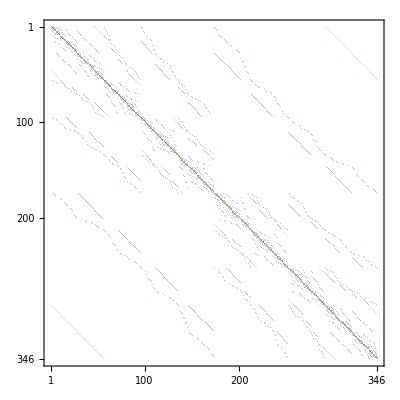

```mathematica
ZeroHamiltonian[g_, alpha_, nQubits_]  := PermHamiltonian[g, alpha, nQubits][[1;;NZero, 1;;NZero]]
ZeroH = ZeroHamiltonian[.2, 1., 12];
MatrixPlot[ZeroH]
```

## Eigenvalue Spectrum of the Sub-Hamiltonian

```mathematica
SubEigs = Eigenvalues[Normal[ZeroH]]
```

{562.657,513.159,502.405,497.899,497.899,493.47,493.47,492.681,492.681,492.681,492.681,491.679,491.679,491.617,481.029,456.132,456.132,456.132,456.132,453.93,453.93,453.93,453.93,451.035,451.035,449.363,449.363,446.947,435.654,435.654,434.79,428.136,427.847,427.847,427.623,427.623,426.273,426.273,424.28,423.731,423.731,423.623,423.623,422.386,422.386,422.386,422.386,421.581,421.557,421.478,421.47,421.47,421.449,421.449,421.449,421.449,421.391,421.391,421.099,421.099,420.955,420.955,420.906,420.856,420.856,420.83,420.82,420.82,419.229,419.229,418.776,418.776,418.776,418.776,418.095,418.095,418.095,418.095,406.863,403.654,403.654,403.357,403.187,403.187,402.496,402.496,401.257,401.026,401.026,400.355,400.355,400.24,400.24,400.24,399.858,399.858,398.173,398.173,397.473,395.649,394.979,394.979,394.738,394.738,389.692,387.099,387.099,385.131,375.24,375.24,369.536,369.536,369.536,369.536,366.078,366.078,364.805,364.805,364.805,364.805,362.7,362.7,358.97,358.97,358.968,358.968,358.056,358.056,358.056,358.056,356.834,354.925,354.925,354.564,354.564,354.564,354.564,354.534,354.334,354.334,353.865,353.865,353.865,353.865,351.82,351.82,351.797,351.797,351.792,351.637,351.637,351.636,351.636,350.246,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.24,350.236,350.236,350.165,350.165,350.161,350.16,350.16,350.16,350.16,350.16,350.16,350.137,350.137,350.134,350.134,350.133,350.083,350.083,350.08,350.035,349.455,349.455,349.455,349.455,348.693,348.693,347.906,347.906,347.881,347.213,347.213,347.039,346.865,346.526,346.526,346.526,346.526,345.775,345.277,345.277,345.277,345.277,343.476,343.476,343.153,343.153,343.153,343.153,341.43,341.43,341.429,341.429,337.7,337.7,336.879,336.879,335.633,335.633,335.633,335.633,330.638,330.638,330.638,330.638,325.24,325.24,311.401,310.174,310.174,309.223,309.223,307.459,303.647,303.647,302.915,302.901,300.97,300.97,300.912,300.24,300.1,299.583,299.452,299.452,298.822,298.822,298.32,298.32,298.128,298.128,297.978,297.978,295.144,295.063,294.656,294.656,286.149,286.149,281.734,281.734,281.734,281.734,280.9,280.9,280.859,279.448,279.448,279.429,279.293,279.238,279.1,279.1,279.1,279.1,279.044,279.044,279.002,279.002,278.93,278.93,278.852,278.852,278.783,278.783,278.113,278.113,278.035,278.035,278.035,278.035,277.96,277.96,277.869,277.869,277.869,277.869,276.189,276.168,276.101,273.214,273.214,267.618,267.618,267.524,267.283,267.283,261.723,249.331,249.331,249.331,249.331,249.07,249.07,249.07,249.07,245.757,245.757,240.881,240.881,208.087,208.087,208.086,208.086,207.239,207.239,206.443,206.233,204.702,204.702,204.702,204.702,200.219,199.586,133.907}

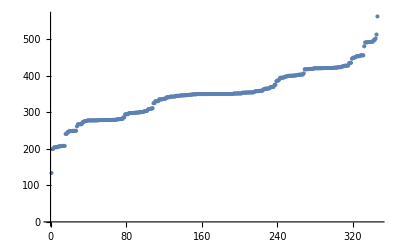

```mathematica
ListPlot[Sort[N[SubEigs]]]
```

{1.,2.,2.00963,2.0779,2.0779,2.0779,2.0779,2.10121,2.1044,2.11652,2.11652,2.12941,2.12941,2.12942,2.12942,2.62874,2.62874,2.70298,2.70298,2.75341,2.75341,2.75341,2.75341,2.75739,2.75739,2.75739,2.75739,2.94606,3.03072,3.03072,3.03439,3.03582,3.03582,3.12103,3.12103,3.16498,3.16599,3.16633,3.1919,3.1919,3.1919,3.1919,3.19328,3.19328,3.19442,3.19442,3.19442,3.19442,3.19561,3.19561,3.20582,3.20582,3.20686,3.20686,3.20806,3.20806,3.20914,3.20914,3.2098,3.2098,3.21064,3.21064,3.21064,3.21064,3.21275,3.21358,3.21564,3.21593,3.21593,3.23743,3.23805,3.23805,3.25075,3.25075,3.25075,3.25075,3.31796,3.31796,3.4475,3.4475,3.45369,3.45492,3.49806,3.49806,3.50035,3.50035,3.50328,3.50328,3.51092,3.51092,3.52051,3.52051,3.52251,3.53038,3.53251,3.54275,3.54363,3.54363,3.57302,3.57324,3.58438,3.58438,3.64243,3.66928,3.66928,3.68376,3.68376,3.70245,3.91315,3.91315,3.99534,3.99534,3.99534,3.99534,4.07139,4.07139,4.07139,4.07139,4.09035,4.09035,4.10286,4.10286,4.15964,4.15964,4.15965,4.15965,4.18588,4.18588,4.18588,4.18588,4.1908,4.1908,4.21823,4.21823,4.21823,4.21823,4.2258,4.23724,4.23724,4.23724,4.23724,4.2424,4.24505,4.2477,4.2477,4.25786,4.25825,4.25825,4.27023,4.27023,4.28184,4.28184,4.28184,4.28184,4.29066,4.29135,4.29139,4.29139,4.29216,4.29217,4.29217,4.29222,4.29222,4.29257,4.29257,4.29257,4.29257,4.29257,4.29257,4.29258,4.29264,4.29264,4.29372,4.29372,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29379,4.29387,4.31505,4.31505,4.31506,4.31506,4.31742,4.31749,4.31749,4.31784,4.31784,4.34898,4.34898,4.34898,4.34898,4.35612,4.35612,4.35916,4.35962,4.35962,4.35962,4.35962,4.36512,4.36512,4.39419,4.41279,4.41279,4.41279,4.41279,4.42668,4.42668,4.4267,4.4267,4.4835,4.4835,4.51555,4.51555,4.51555,4.51555,4.53492,4.53492,4.58758,4.58758,4.58758,4.58758,4.67442,4.67442,4.82502,4.85498,4.85498,4.89447,4.9713,4.9713,4.97497,4.97497,4.98517,5.01293,5.02359,5.02359,5.04925,5.04925,5.05506,5.05506,5.05506,5.05682,5.05682,5.06703,5.06703,5.07054,5.08941,5.08941,5.09993,5.09993,5.10252,5.10704,5.10704,5.1559,5.32691,5.32691,5.32691,5.32691,5.33729,5.33729,5.33729,5.33729,5.34418,5.34418,5.3684,5.3684,5.36855,5.36895,5.36895,5.36971,5.37045,5.37045,5.37265,5.37265,5.3771,5.3771,5.37798,5.37798,5.37798,5.37798,5.37829,5.37829,5.37843,5.37963,5.37999,5.39224,5.39224,5.39224,5.39224,5.41109,5.41109,5.41273,5.41273,5.42109,5.45143,5.45143,5.47198,5.47198,5.47539,5.47539,5.47979,5.5811,5.59426,5.59426,5.7662,5.80298,5.80298,5.82844,5.82844,5.87253,5.87253,5.87253,5.87253,5.90605,5.90605,5.90605,5.90605,6.28512,6.44633,6.44727,6.44727,6.46253,6.46253,6.46253,6.46253,6.47454,6.47454,6.54198,6.54198,6.61058,6.77432,7.52795}

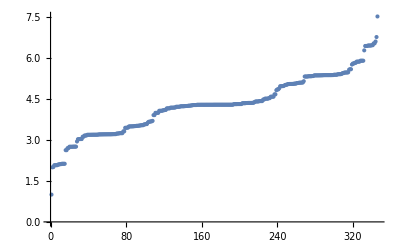

```mathematica
EigenSpectra:= Sort[SubEigs]
EigenSpectra//N;
lambda0= EigenSpectra [[1]]//N;
lambda1 = EigenSpectra [[2]]//N;
NormalizedSpectra =(1/(lambda1 - lambda0))( EigenSpectra+ lambda1 - 2 lambda0)//N
ListPlot[NormalizedSpectra]
```

## What if we change the value of g?

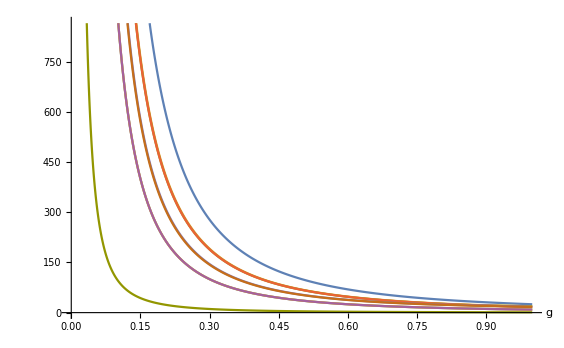

```mathematica
ListPlot[Transpose[Table[Eigenvalues[ZeroHamiltonian[g, 2, 6]], {g, 0.01, 1, 0.001}]], Joined->True, DataRange->{0.01, 1}, AxesLabel-> {"g", ""}]
```

# Continuum Model Change varables preserving the computors (and redefing charge!) H = (2/g^2)p^2 + (1/g^2) (1 - Cos[theta]) + p12^2 +p23^2 + p31^2 with theta = theta1, +theta2 + theta3 and p = (E1 +E2 + E3)/ 3 External flux/gauge opeartors pij = E_i - E_j

```mathematica
Dia[n_]:= Table[i^2,{i,-n,n}]
Dia[5]
```

{25,16,9,4,1,0,1,4,9,16,25}

# This initializs the matrix for one plaquette, where a is the strength of the magnetic part relative to electric part.

```mathematica
Mat[n_,g_]:=
Table[ (g^2/2)KroneckerDelta[i,j] i^2+ (1/g^2)( 2 KroneckerDelta[i,j] -  KroneckerDelta[i,j+1]-KroneckerDelta[i,j-1]),{i,-n,n},{j,-n,n}]
MatrixForm[Mat[4,g]]
```

(2/g^2+8 g^2 | -1/g^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/g^2 | 2/g^2+(9 g^2)/2 | -1/g^2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/g^2 | 2/g^2+2 g^2 | -1/g^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/g^2 | 2/g^2+g^2/2 | -1/g^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/g^2 | 2/g^2 | -1/g^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+g^2/2 | -1/g^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+2 g^2 | -1/g^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+(9 g^2)/2 | -1/g^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+8 g^2)

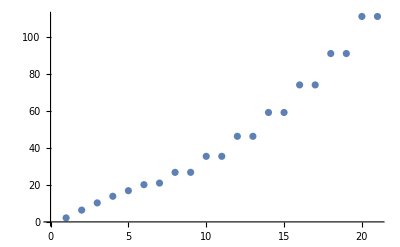

```mathematica
ListPlot[Sort[Re[Eigenvalues[(2/0.795^2)Mat[10,0.795]]],Less]]
```

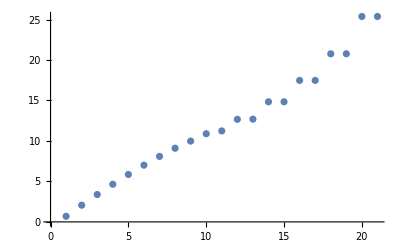

```mathematica
ListPlot[Sort[Re[Eigenvalues[Mat[10,0.6]]],Less]]
```

```mathematica
Dat=Table[Sort[Re[Eigenvalues[Mat[18,g], Method->"Banded"]],Less],{g,0.1,2.1,0.05}];
```

```mathematica
Here one can see how the level degenracy is split as we increase the magnetic term
as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.37,-71.13}]
```

as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.35,-71.08}]

as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.37,-71.13}]

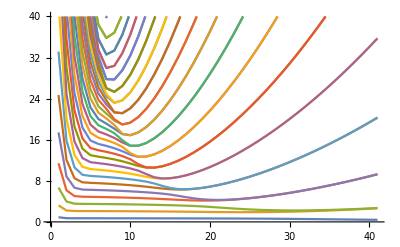

```mathematica
ListPlot[Transpose[Dat], Joined->True,PlotRange->{0,40}]
```

```mathematica
Length[Dat]
```

41

```mathematica
Here is the result with plaquette = 0 and with plaquette = 20, showing that the low energy degrees of freedom have a linear spectrum once magnetic term is strong
```

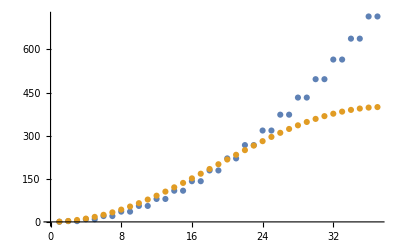

```mathematica
ListPlot[{Dat[[41]],Dat[[1]]}]
```

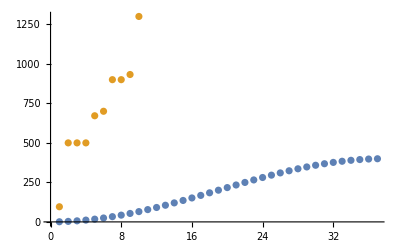

```mathematica
ListPlot[{Dat[[1]], Sort[Eigenvalues[ZeroHamiltonian[0.1, 1, 6]]]}]
```

```mathematica
Eigenvalues[KroneckerProduct[Sigma[1], Sigma[1], Sigma[1]]-KroneckerProduct[Sigma[1], Sigma[2], Sigma[2]] - KroneckerProduct[Sigma[2], Sigma[1], Sigma[2]]-KroneckerProduct[Sigma[2], Sigma[2], Sigma[1]]]
```

{-4,4,0,0,0,0,0,0}